# Εργασία 2η

```mathematica
(*
ResourceFunction["MaTeXInstall"];
ResourceFunction["MaTeXInstall"][];
Needs["MaTeX`"];
*)
```

## 1η Άσκηση

Έστω μία τυχαία μεταβλητή X η οποία ακολουθεί την κατανομή Rayleigh, με πυκνότητα πιθανότητας f(x|σ) = x/σ^2e^(-x^2/2 σ^2), x≥0 και ένα σύνολο 10 ανεξαρτήτων τιμών αυτής της μεταβλητής Σ={0.96, 1.12, 0.85, 1.02, 1.58, 1.86, 0.79, 0.82, 0.45, 1.52}. 
a. Να βρείτε αναλυτικά την εκτίμηση της παραμέτρου σ̂ χρησιμοποιώντας τη μέθοδο μέγιστης πιθανοφάνειας. 
b. Να υπολογίσετε το σφάλμα της εκτίμησής σας χρησιμοποιώντας την προσεγγιστική (Hessian) και την ακριβή μέθοδο. 
c. Να παραστήσετε γραφικά τη συνάρτηση lnL(σ), όπου L είναι η πιθανοφάνεια του δείγματος Σ και στο ίδιο διάγραμμα να δείξετε την παραβολική προσέγγιση στο σημείο του μεγίστου

Λύση

```mathematica
ClearAll["Global`*"];
```

Οι τιμές του Χ

```mathematica
S =  {0.96,1.12,0.85,1.02,1.58,1.86,0.79,0.82,0.45,1.52};
```

Η PDF της Rayleigh

```mathematica
Rayleigh=PDF[RayleighDistribution[σ],X]
```

Piecewise[{{(ⅇ^(-X^2/(2 σ^2)) X)/σ^2, X>0}, {0, True}}]

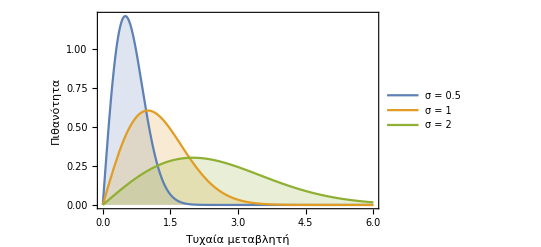

```mathematica
Plot[Table[PDF[RayleighDistribution[σ],x],{σ,{.5,1,2}}]//Evaluate,{x,0,6},Filling->Axis,PlotRange->All,PlotLegends->{"σ = 0.5","σ = 1","σ = 2"},Frame->True,FrameLabel->{"Τυχαία μεταβλητή","Πιθανότητα"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

Η Log Likelihood της κατανομής

```mathematica
f= LogLikelihood[RayleighDistribution[σ],S]
```

0.193821-6.85215/σ^2-20 Log[σ]

```mathematica
FindMaximum[f,σ]
```

{-6.02595,{σ→0.827777}}

Η Hessian της κατανομής είναι

```mathematica
σhat=σ/.FindMaximum[f,σ][[2]]
```

0.827777

```mathematica
H = D[f,{σ ,2}]/. σ -> σhat
```

-58.3758

Έτσι το σφάλμα της εκτίμησης προσεγγιστικά είναι:

```mathematica
Subscript[σ, θ]=Sqrt[-H]^(-1)
```

0.130883

Ενώ με την ακριβή μέθοδο:

```mathematica
σacc=StandardDeviation[S]/Sqrt[Length[S]]
```

0.136227

Γραφική Παράσταση της Log-Likelihood

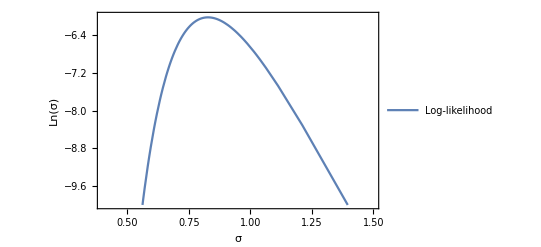

```mathematica
p1=Plot[LogLikelihood[RayleighDistribution[σ],S],{σ,0,10},Frame->True,FrameLabel->{"σ","Ln(σ)"},LabelStyle->{FontFamily->"Times New Roman",20},PlotRange->{{0.4,1.5},{-10,-6}},PlotLegends->{"Log-likelihood"}]
```

Παραβολική προσέγγιση της Log-Likelihood

```mathematica
L = LogLikelihood[RayleighDistribution[σhat],S] + (1/2)*( H)*(σ - σhat)^2
FindMaximum[L,σ]
```

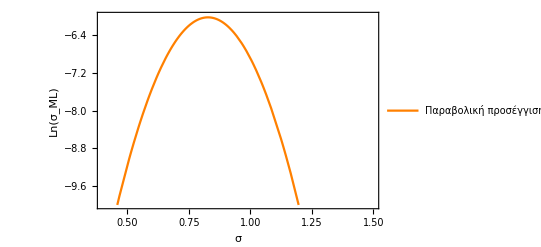

```mathematica
p2=Plot[L,{σ,-5,10},PlotStyle -> Orange,Frame->True,FrameLabel->{"σ","Ln(σ_ML)"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"Παραβολική προσέγγιση"},PlotRange->{{0.4,1.5},{-10,-6}}]
```

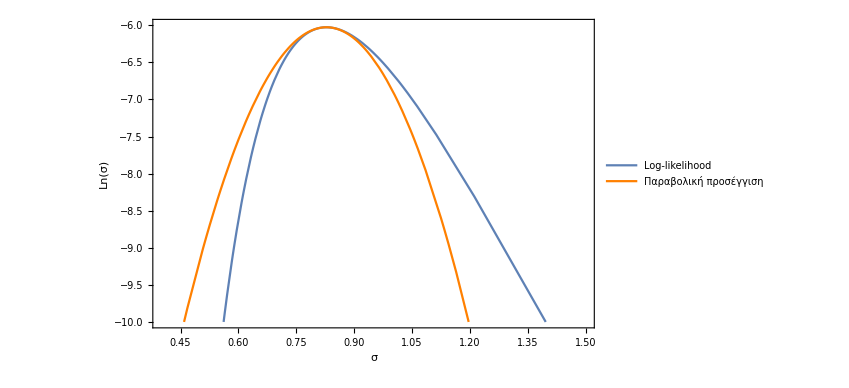

```mathematica
Show[p1,p2]
```

## 2η Άσκηση

Θεωρήστε την κατανομή Poisson με παράμετρο μ = 4. 
a. Να παράξετε Ν = 10, 20, 50 τυχαίους αριθμούς από αυτή την κατανομή. 
b. Για κάθε σύνολο αριθμών του ερωτήματος (a) να υπολογίσετε την εκτίμηση μέγιστης πιθανοφάνειας μ̂ ± σ_(μ̂) και να παραστήσετε γραφικά τη συνάρτηση lnL(μ) - lnL(μ̂) (στο ίδιο διάγραμμα και τα τρία σύνολα). 
c. Να επαναλάβετε τα βήματα (a) και (b) 1000 φορές (χωρίς τη γραφική παράσταση του (b)) και να δείξετε την κατανομή των μ̂, σ_(μ̂)  που παίρνετε από κάθε ψευδοπείραμα. Ποιά είναι η μέση τιμή και η διασπορά της εκτίμησης μέγιστης πιθανοφάνειας ανάλογα με το μέγεθος του δείγματος (10, 20, 50); Σχολιάστε το αποτέλεσμα. 
d. Να παραστήσετε την κατανομή της μεταβλητής z = (μ̂-μ)/(σ_(μ̂)) στα ψευδοπειράματα (ένα ιστόγραμμα για κάθε Ν). Τη μορφή έχει;

Λύση

```mathematica
ClearAll["Global`*"];
```

Οι τυχαίοι αριθμοί που θα παραχθούν:

```mathematica
n={10,20,50};
```

Παραγωγή των τυχαίων αριθμών:

```mathematica
PD10=RandomVariate[PoissonDistribution[4],n[[1]]];
```

```mathematica
PD20 =RandomVariate[PoissonDistribution[4],n[[2]]];
```

```mathematica
PD50 =RandomVariate[PoissonDistribution[4],n[[3]]];
```

Το ιστόγραμμα των 3 περιπτώσεων:

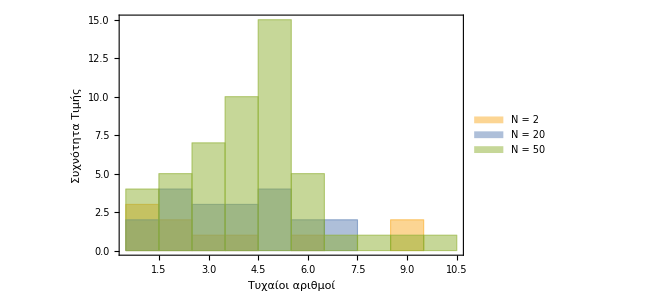

```mathematica
Histogram[{PD10,PD20,PD50},50,ChartLegends -> Placed[{"N = 2", "N = 20",  "N = 50"}, Right],Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

Η Log-Likelihood κάθε περίπτωσης

```mathematica
FPD10= LogLikelihood[PoissonDistribution[4],PD10];
FPD20= LogLikelihood[PoissonDistribution[4],PD20];
FPD50= LogLikelihood[PoissonDistribution[4],PD50];
```

H Log-Likelihood για κάθε N

```mathematica
fPD10 = LogLikelihood[PoissonDistribution[μ],PD10]//N
```

-38.539-10. μ+38. Log[μ]

```mathematica
fPD20 = LogLikelihood[PoissonDistribution[μ],PD20]//N
```

-67.0408-20. μ+77. Log[μ]

```mathematica
fPD50 = LogLikelihood[PoissonDistribution[μ],PD50]//N
```

-199.533-50. μ+214. Log[μ]

Εκτίμηση μέγιστης πιθανοφάνειας:

```mathematica
FindMaximum[fPD10,μ]
```

{-25.809,{μ→3.8}}

```mathematica
FindMaximum[fPD20,μ]
```

{-40.2392,{μ→3.85}}

```mathematica
FindMaximum[fPD50,μ]
```

{-102.387,{μ→4.28}}

Η Hessian της κατανομής είναι

```mathematica
μhatPD10=μ/.FindMaximum[fPD10,μ][[2]];
HfPD10 = D[fPD10,{μ ,2}]/. μ -> μhatPD10;
```

```mathematica
μhatPD20=μ/.FindMaximum[fPD20,μ][[2]];
HfPD20 = D[fPD20,{μ ,2}]/. μ -> μhatPD20;
```

```mathematica
μhatPD50=μ/.FindMaximum[fPD50,μ][[2]];
HfPD50 = D[fPD50,{μ ,2}]/. μ -> μhatPD50;
```

Έτσι το σφάλμα της εκτίμησης προσεγγιστικά είναι:

```mathematica
Subscript[σ, μPD10]=Sqrt[-HfPD10]^(-1)
```

0.616441

```mathematica
Subscript[σ, μPD20]=Sqrt[-HfPD20]^(-1)
```

0.438748

```mathematica
Subscript[σ, μPD50]=Sqrt[-HfPD50]^(-1)
```

0.292575

Πλοτάρισμα των συναρτήσεων

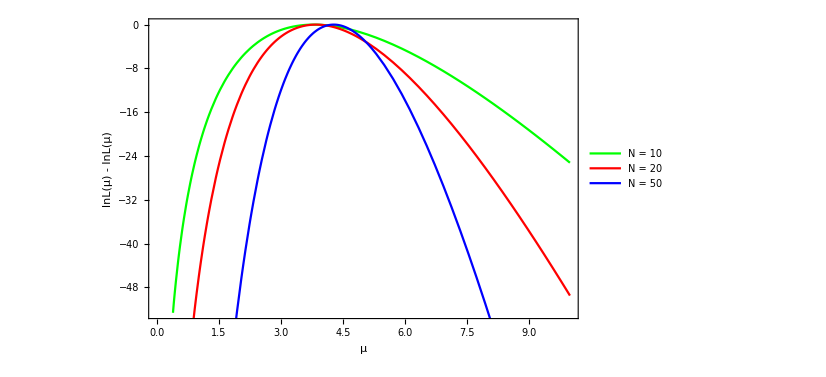

```mathematica
pPD10 = Plot[fPD10- LogLikelihood[PoissonDistribution[μhatPD10],PD10],{μ,0,10},PlotStyle->Green,Frame->True,FrameLabel->{"μ","lnL(μ) - lnL(μ)"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"N = 10"}];
pPD20 = Plot[fPD20- LogLikelihood[PoissonDistribution[μhatPD20],PD20],{μ,0,10},PlotStyle->Red,Frame->True,FrameLabel->{"μ","lnL(μ) - lnL(μ)"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"N = 20"}];
pPD50 = Plot[fPD50- LogLikelihood[PoissonDistribution[μhatPD50],PD50],{μ,0,10},PlotStyle->Blue,Frame->True,FrameLabel->{"μ","lnL(μ) - lnL(μ)"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"N = 50"}];
Show[pPD10,pPD20,pPD50]
```

Επανάληψη για 1000 φορές

```mathematica
TPD10=ParallelTable[RandomVariate[PoissonDistribution[4],n[[1]]],{i,1,1000}];
```

```mathematica
TPD20=ParallelTable[RandomVariate[PoissonDistribution[4],n[[2]]],{i,1,1000}];
```

```mathematica
TPD50=ParallelTable[RandomVariate[PoissonDistribution[4],n[[3]]],{i,1,1000}];
```

```mathematica
μhatPD10Table=ParallelTable[μ/.FindMaximum[LogLikelihood[PoissonDistribution[μ],TPD10[[i]]],μ,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->100][[2]],{i,1,1000}];
HfPD10Table =ParallelTable[ D[LogLikelihood[PoissonDistribution[μ],TPD10[[i]]],{μ ,2}]/. μ -> μhatPD10Table[[i]],{i,1,1000}];
Subscript[Tσ, μPD10]=ParallelTable[Sqrt[-HfPD10Table[[i]]]^(-1),{i,1,1000}];
```

```mathematica
μhatPD20Table=ParallelTable[μ/.FindMaximum[LogLikelihood[PoissonDistribution[μ],TPD20[[i]]],μ,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->100][[2]],{i,1,1000}];
HfPD20Table =ParallelTable[ D[LogLikelihood[PoissonDistribution[μ],TPD20[[i]]],{μ ,2}]/. μ -> μhatPD20Table[[i]],{i,1,1000}];
Subscript[Tσ, μPD20]=ParallelTable[Sqrt[-HfPD20Table[[i]]]^(-1),{i,1,1000}];
```

```mathematica
μhatPD50Table=ParallelTable[μ/.FindMaximum[LogLikelihood[PoissonDistribution[μ],TPD50[[i]]],μ,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->100][[2]],{i,1,1000}];
HfPD50Table =ParallelTable[ D[LogLikelihood[PoissonDistribution[μ],TPD50[[i]]],{μ ,2}]/. μ -> μhatPD50Table[[i]],{i,1,1000}];
Subscript[Tσ, μPD50]=ParallelTable[Sqrt[-HfPD50Table[[i]]]^(-1),{i,1,1000}];
```

```mathematica
MeanμhatPD10Table = Mean[μhatPD10Table]
VarμhatPD10Table = Variance[μhatPD10Table]
```

4.012599999999999999999555009816190523018631452752387075263315828626928515651758884906028682078661568

0.38260384384384384384405378006612841970813969472104492716641795897362277667809090884543604892895333

```mathematica
MeanμhatPD20Table = Mean[μhatPD20Table]
VarμhatPD20Table =  Variance[μhatPD20Table]
```

3.974049999999999999999666053916841412658239075881537030889430117169088974008231946770316358390636184

0.20350760510510510510495575736260078244825350360003308757935169220434931195727240792217241356822661

```mathematica
MeanμhatPD50Table = Mean[μhatPD50Table]
VarμhatPD50Table =  Variance[μhatPD50Table]
```

4.00315999999999999999987461046695377553604611412806881714809764148400533168767890050473653709619811

0.078693507907907907907767313827680869699884360607225976063912178059124446205250312057261751119987348

Υπολογισμός και ιστόγραμμα μεταβλητής z

```mathematica
z10 =ParallelTable[- (μhatPD10Table[[i]] -Mean[μhatPD10Table])/(Subscript[Tσ, μPD10][[i]]),{i,1,1000}];
```

```mathematica
z20 =ParallelTable[- (μhatPD20Table[[i]] -Mean[μhatPD20Table])/(Subscript[Tσ, μPD20][[i]]),{i,1,1000}];
```

```mathematica
z50 =ParallelTable[- (μhatPD50Table[[i]] -Mean[μhatPD50Table])/(Subscript[Tσ, μPD50][[i]]),{i,1,1000}];
```

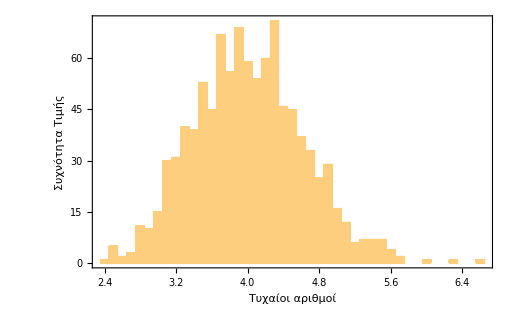

```mathematica
histμhatPD10=Histogram[μhatPD10Table,30,Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

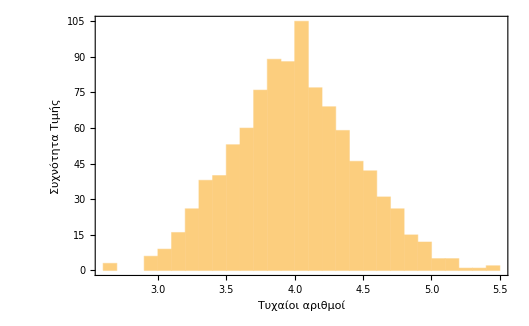

```mathematica
histμhatPD20=Histogram[μhatPD20Table,30,Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

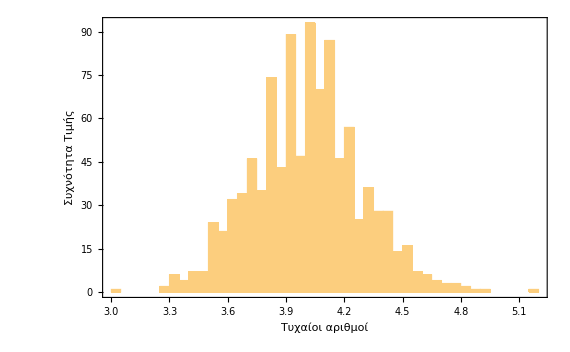

```mathematica
histμhatPD50=Histogram[μhatPD50Table,30,Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

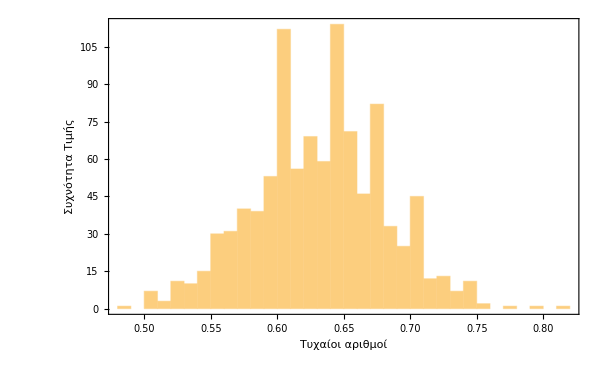

```mathematica
Subscript[histTσ, μPD10]=Histogram[Subscript[Tσ, μPD10],30,Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

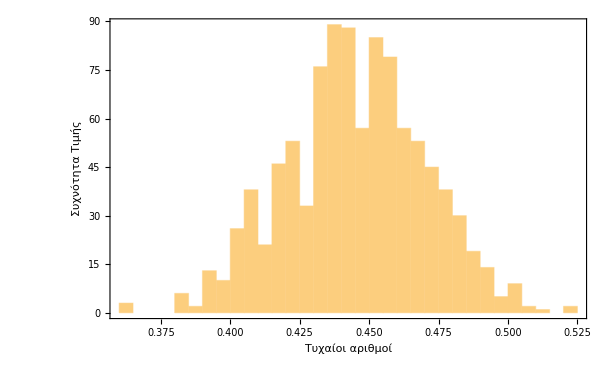

```mathematica
Subscript[histTσ, μPD20]=Histogram[Subscript[Tσ, μPD20],30,Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

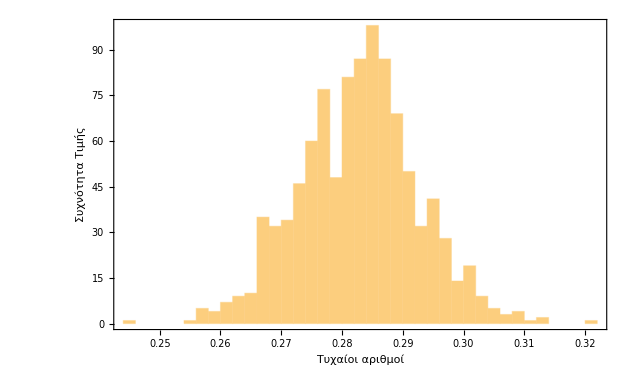

```mathematica
Subscript[histTσ, μPD50]=Histogram[Subscript[Tσ, μPD50],30,Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

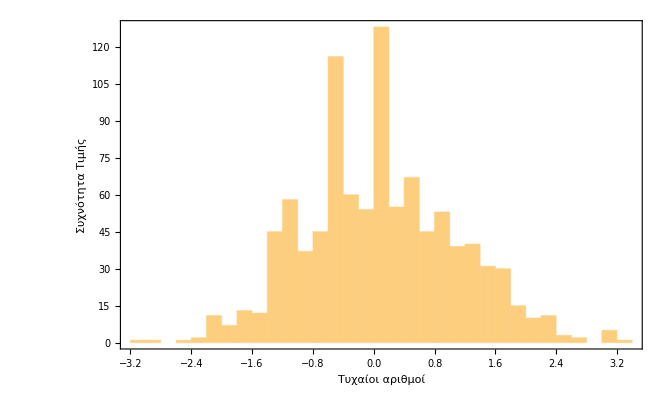

```mathematica
hist10=Histogram[z10,30,Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

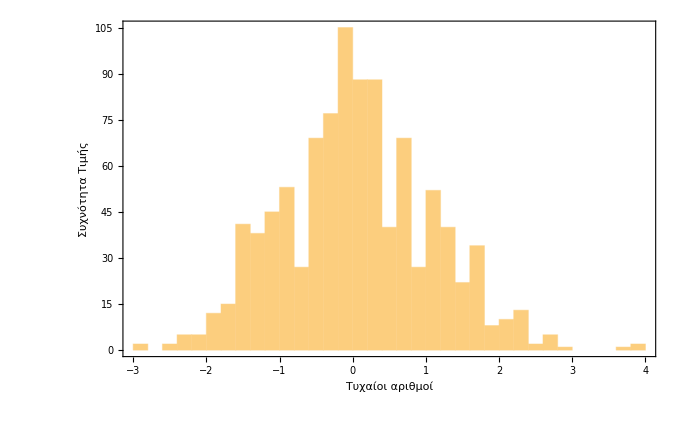

```mathematica
hist20=Histogram[z20,30,Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

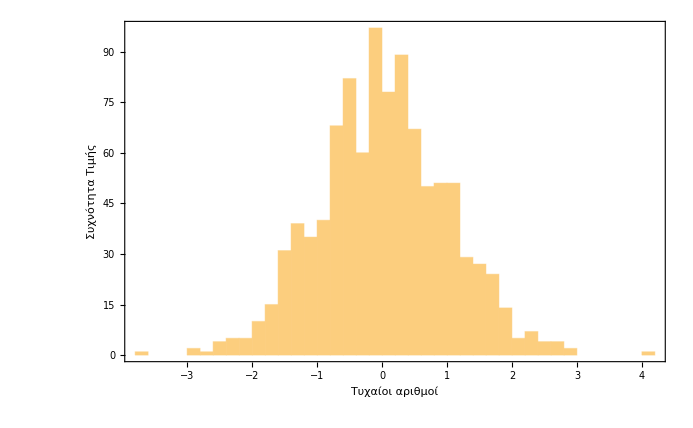

```mathematica
hist50=Histogram[z50,30,Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

## 3η Άσκηση

Τα πειράματα ATLAS και CMS στο CERN έχουν πραγματοποιήσει μετρήσεις της ενεργού διατομής παραγωγής ζευγών top-anti-top quark σε συγκρούσεις πρωτονίων με ενέργεια κέντρου μάζας 13 TeV σε διαφορετικές τελικές καταστάσεις. Οι μετρήσεις δίνονται στον παρακάτω πίνακα: 
Μέτρηση  | σ(pb) | stat.unc.(pb) | syst.unc.(pb) | lumi.unc.(pb)
ATLAS dilepton | 818 | 8 | 27 | 19
CMS dilepton | 815 | 9 | 38 | 19
CMS l+jets | 888 | 2 | 27 | 20
CMS hadronic | 834 | 25 | 118 | 23
a. Να κατασκευάσετε τον συνολικό πίνακα συνδιασποράς των μετρήσεων αυτών αν υποθέσουμε ότι: 
1) οι στατιστικές αβεβαιότητες (δεύτερη στήλη) είναι ασυσχέτιστες, 
2) οι συστηματικές αβεβαιότητες (τρίτη στήλη) μεταξύ των μετρήσεων του CMS έχουν 40% συσχέτιση και μεταξύ των μετρήσεων του CMS και του ATLAS 20%,
 3) οι αβεβαιότητες στην φωτεινότητα (τέταρτη στήλη) είναι 100% συσχετισμένες μεταξύ των μετρήσεων του CMS και 90% μεταξύ των μετρήσεων του CMS και του ATLAS. 
b. Να συνδυάσετε τις παραπάνω μετρήσεις σε ένα αποτέλεσμα με τη μέθοδο BLUE και χρησιμοποιώντας τον πίνακα συνδιασποράς του (a) ερωτήματος.

Λύση

```mathematica
ClearAll["Global`*"];
```

```mathematica
u = {1,1,1,1};
uM1 = {{1,1,1,1}};
```

```mathematica
u//MatrixForm
```

(1
1
1
1)

```mathematica
uM1//MatrixForm
```

(1 | 1 | 1 | 1)

Οι μετρήσεις των πειραμάτων είναι:

```mathematica
CS = {818,815,888,834};
```

Η μέση τιμή των μετρήσεων είναι:

```mathematica
Mean[CS]//N
```

838.75

Πίνακας συνδιασποράς για τη 2η στήλη:

```mathematica
STU1={8,9,2,25};
```

```mathematica
ρ12 = 0;
```

```mathematica
VSTUTOT = {
{STU1[[1]]^2,ρ12*STU1[[1]]*STU1[[2]],ρ12*STU1[[1]]*STU1[[3]],ρ12*STU1[[1]]*STU1[[4]]},
{ρ12*STU1[[1]]*STU1[[2]],STU1[[2]]^2,ρ12*STU1[[3]]*STU1[[2]],ρ12*STU1[[4]]*STU1[[2]]},
{ρ12*STU1[[1]]*STU1[[3]],ρ12*STU1[[2]]*STU1[[2]],STU1[[3]]^2,ρ12*STU1[[4]]*STU1[[2]]},
{ρ12*STU1[[1]]*STU1[[4]],ρ12*STU1[[2]]*STU1[[4]],ρ12*STU1[[3]]*STU1[[4]],STU1[[4]]^2}
};
```

```mathematica
%//MatrixForm
```

(64 | 0 | 0 | 0
0 | 81 | 0 | 0
0 | 0 | 4 | 0
0 | 0 | 0 | 625)

Πίνακας συνδιασποράς για τη 3η στήλη:

```mathematica
ρ3CMS=0.4 ;
ρ3CMSATLAS = 0.2;
STU3={27,38,27,118};
```

```mathematica
VSYSTTOT=
{
{STU3[[1]]^2,ρ3CMSATLAS*STU3[[1]]*STU3[[2]],ρ3CMSATLAS*STU3[[1]]*STU3[[3]],ρ3CMSATLAS*STU3[[1]]*STU3[[4]]},
{ρ3CMSATLAS*STU3[[1]]*STU3[[2]],STU3[[2]]^2,ρ3CMS*STU3[[3]]*STU3[[2]],ρ3CMS*STU3[[4]]*STU3[[2]]},
{ρ3CMSATLAS*STU3[[1]]*STU3[[3]],ρ3CMS*STU3[[2]]*STU3[[2]],STU3[[3]]^2,ρ3CMS*STU3[[4]]*STU3[[2]]},
{ρ3CMSATLAS*STU3[[1]]*STU3[[4]],ρ3CMS*STU3[[2]]*STU3[[4]],ρ3CMS*STU3[[3]]*STU3[[4]],STU3[[4]]^2}
};
```

```mathematica
%//MatrixForm
```

(729 | 205.2 | 145.8 | 637.2
205.2 | 1444 | 410.4 | 1793.6
145.8 | 577.6 | 729 | 1793.6
637.2 | 1793.6 | 1274.4 | 13924)

Πίνακας συνδιασποράς για τη 4η στήλη:

```mathematica
ρ4CMS=1;
ρ4CMSATLAS = 0.9;
STU4={19,19,20,23};
```

```mathematica
VLUMTOT=
{
{STU4[[1]]^2,ρ4CMSATLAS*STU4[[1]]*STU4[[2]],ρ4CMSATLAS*STU4[[1]]*STU4[[3]],ρ4CMSATLAS*STU4[[1]]*STU4[[4]]},
{ρ4CMSATLAS*STU4[[1]]*STU4[[2]],STU4[[2]]^2,ρ4CMS*STU4[[3]]*STU4[[2]],ρ4CMS*STU4[[4]]*STU4[[2]]},
{ρ4CMSATLAS*STU4[[1]]*STU4[[3]],ρ4CMS*STU4[[2]]*STU4[[2]],STU4[[3]]^2,ρ4CMS*STU4[[4]]*STU4[[2]]},
{ρ4CMSATLAS*STU4[[1]]*STU4[[4]],ρ4CMS*STU4[[2]]*STU4[[4]],ρ4CMS*STU4[[3]]*STU4[[4]],STU4[[4]]^2}
};
```

```mathematica
VLUMTOT//MatrixForm
```

(361 | 324.9 | 342. | 393.3
324.9 | 361 | 380 | 437
342. | 361 | 400 | 437
393.3 | 437 | 460 | 529)

Ο συνολικός πίνακας συνδιασποράς:

```mathematica
VTOT= VSTUTOT+VSYSTTOT+VLUMTOT;
```

```mathematica
VTOT//MatrixForm
```

(1154 | 530.1 | 487.8 | 1030.5
530.1 | 1886 | 790.4 | 2230.6
487.8 | 938.6 | 1133 | 2230.6
1030.5 | 2230.6 | 1734.4 | 15078)

Ο αντίστροφος συνολικός πίνακας συνδιασποράς:

```mathematica
VTOTM1=Inverse[VSTUTOT+VSYSTTOT+VLUMTOT];
```

```mathematica
VTOTM1//MatrixForm
```

(0.00108161 | -0.000110618 | -0.000388343 | -1.07549×10^-7
-0.000158223 | 0.000859841 | -0.000457057 | -0.0000487732
-0.000303992 | -0.000554773 | 0.001607 | -0.000134887
-0.0000155477 | -0.0000558278 | -0.0000906936 | 0.0000890604)

Χρήση της γενικευμένης μεθόδου BLUE:

```mathematica
VTOTM1.u
```

{0.000582546,0.000195789,0.000613345,-0.0000730088}

```mathematica
x=uM1.VTOTM1.u
```

{0.00131867}

```mathematica
w = VTOTM1.u/(x[[1]])
```

{0.441767,0.148474,0.465124,-0.0553654}

```mathematica
wT = Transpose[w]
```

{0.441767,0.148474,0.465124,-0.0553654}

```mathematica
w//MatrixForm
```

(0.441767
0.148474
0.465124
-0.0553654)

```mathematica
wT//MatrixForm
```

(0.441767
0.148474
0.465124
-0.0553654)

```mathematica
σθhat2 = wT.VTOT.w
```

758.339

```mathematica
θhat = Sum[CS[[i]]*w[[i]],{i,1,4}]//N
```

849.227

```mathematica
σθhat = Sqrt[%]
```

29.1415

## 4η Άσκηση

Έστω ένα φυσικό μέγεθος το οποίο μειώνεται εκθετικά με τον χρόνο y = y_0e^(-t/τ) και διαθέτουμε το παρακάτω σύνολο μετρήσεων, όπου μπορούμε να αγνοήσουμε το σφάλμα στη μέτρηση του χρόνου. 
Α/Α | t (min) | y | σ_y
1 | 1 | 69.4 | 13.9
2 | 2 | 40.8 | 8.2
3 | 3 | 44.4 | 8.9
4 | 4 | 27.7 | 5.5
5 | 5 | 17.1 | 3.4
6 | 6 | 12.3 | 2.5
7 | 7 | 7.8 | 1.6
8 | 8 | 5.9 | 1.2
9 | 9 | 7.2 | 1.4
10 | 10 | 3.9 | 0.8
a. Να υπολογίσετε τις σταθερές y_0 και τ καθώς και τον πίνακα διασποράς αυτών με τη βοήθεια του εκτιμητή χ^2. (Πραγματοποιήστε κατάλληλο μετασχηματισμό ώστε να μπορέσετε να χρησιμοποιήσετε τους τύπους της γραμμικής παλινδρόμησης.) 
b. Να υπολογίσετε την τιμή και την αβεβαιότητα της ποσότητας y για t = 15 min. 
c. Να παραστήσετε στο ίδιο διάγραμμα τo σύνολο των μετρήσεων, την πρόβλεψη (προσαρμογή) του ερωτήματος (a), καθώς και την ±1σ ζώνη αβεβαιότητας αυτής (για την απεικόνιση της ζώνης αυτής να θεωρήσετε έναν ικανό αριθμό σημείων στα οποία να υπολογίσετε την πρόβλεψη και το σφάλμα της και τα οποία όταν αποτυπωθούν σε ένα γράφημα θα δώσουν την εν λόγω ζώνη).

Λύση

```mathematica
ClearAll["Global`*"];
```

```mathematica
inches=72;
```

```mathematica
T=Table[i,{i,1,10}];
Y = {69.6,40.8,44.4,27.7,17.1,12.3,7.8,5.9,7.2,3.9};
```

```mathematica
σY = {13.9,8.2,8.9,5.5,3.4,2.5,1.6,1.2,1.4,0.8};
```

```mathematica
data2 = Table[{T[[i]],Log[Y[[i]]]},{i,1,Length[Y]}];
```

```mathematica
data1 = Table[{T[[i]],PlusMinus[Y[[i]],σY[[i]]]},{i,1,Length[Y]}]
```

{{1,69.6±13.9},{2,40.8±8.2},{3,44.4±8.9},{4,27.7±5.5},{5,17.1±3.4},{6,12.3±2.5},{7,7.8±1.6},{8,5.9±1.2},{9,7.2±1.4},{10,3.9±0.8}}

```mathematica
data = Transpose[{Y,σY}]/.{a_,d_}:>Around[a,d];
```

```mathematica
w = Table[1/(1/(Y[[i]])^2σY[[i]]^2),{i,1, Length[σY]}]
```

{25.072,24.7567,24.8878,25.365,25.295,24.2064,23.7656,24.1736,26.449,23.7656}

Από τους τύπους της γραμμικής παλινδρόμησης έχουμε για τη κλίση

```mathematica
beta = (Sum[w[[i]]*Log[Y[[i]]]*T[[i]],{i,1,10}]*Sum[w[[i]],{i,1,10}]- (Sum[w[[i]]T[[i]],{i,1,10}]*Sum[w[[i]]Log[Y[[i]]],{i,1,10}]))/(Sum[w[[i]]T[[i]]^2,{i,1,10}]*Sum[w[[i]],{i,1,10}] - Sum[w[[i]]T[[i]],{i,1,10}]^2)
```

-0.315884

και για τη σταθερά

```mathematica
alpha = (Sum[w[[i]]Log[Y[[i]]],{i,1,10}]*Sum[w[[i]]T[[i]]^2,{i,1,10}] -Sum[w[[i]]*Log[Y[[i]]]*T[[i]],{i,1,10}] *Sum[w[[i]]T[[i]],{i,1,10}])/(Sum[w[[i]],{i,1,10}]* Sum[w[[i]]T[[i]]^2,{i,1,10}] - Sum[w[[i]]T[[i]],{i,1,10}]^2)
```

4.49919

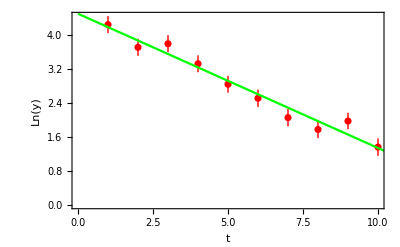

```mathematica
p1=Show[ListPlot[Log[data],PlotRange->Automatic,PlotStyle->Red],Plot[ alpha + beta*t,{t,0,15},PlotStyle->Green],Frame->True,FrameLabel->{"t","Ln(y)"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

Από την συνάρτηση y = y_0e^(-t/τ) που λογαριθμίσαμε για να κάνουμε τη γραμμική παλινδρόμηση έχουμε για τις σταθερές

```mathematica
y0 = E^(alpha)
```

89.9446

```mathematica
τ =-1/beta
```

3.16572

```mathematica
fexp[t_]:= y0*Exp[-t/τ]
```

```mathematica
fexp[15]
```

0.787363

```mathematica
E^(0.7873631477666426)
```

2.19759

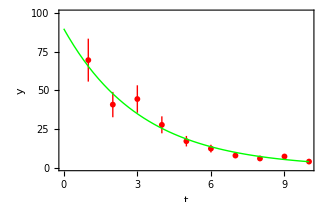

```mathematica
p2=Show[ListPlot[data1,PlotRange->{{0,10},{0,100}},PlotStyle->Red],Plot[fexp[t],{t,0,10},PlotRange->{{0,15},{0,100}},PlotStyle->{Thick,Green}],Frame->True,FrameLabel->{"t","y"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

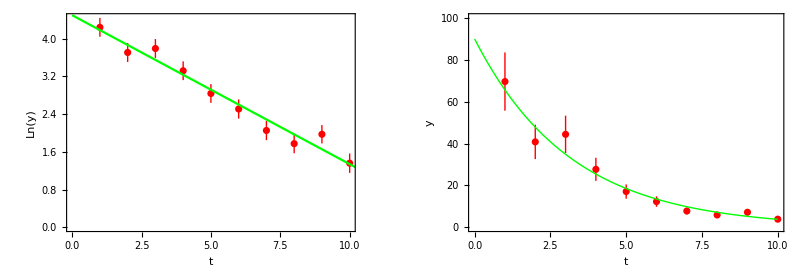

```mathematica
g1=GraphicsRow[{p1,p2}]
Export["ex4-1.png",Show[g1,ImageSize->12 inches]];
```

Για t = 15 min, το y έχει τιμή:

```mathematica
f[t_]:= alpha + beta*t;
E^(f[15])
```

0.787363

```mathematica
f[15]
```

-0.239066

```mathematica
f[0]
```

4.49919

```mathematica
E^(f[0])
```

89.9446

Ο συντελεστής συσχέτισης και τα σφάλματα των a και b είναι

```mathematica
Subscript[ρ, ab] = -(Sum[w[[i]]T[[i]],{i,1,10}] )/(Sqrt[Sum[w[[i]],{i,1,10}]]*Sqrt[Sum[w[[i]]T[[i]]^2,{i,1,10}] ])
```

-0.885662

```mathematica
σb= Sqrt[Sum[w[[i]]T[[i]]^2,{i,1,10}] /(Sum[w[[i]],{i,1,10}] Sum[w[[i]]T[[i]]^2,{i,1,10}]-Sum[w[[i]]T[[i]],{i,1,10}]^2)]
```

0.136829

```mathematica
σa = Sqrt[Sum[w[[i]],{i,1,10}]/(Sum[w[[i]],{i,1,10}] *Sum[w[[i]]T[[i]]^2,{i,1,10}]-Sum[w[[i]]T[[i]],{i,1,10}]^2)]
```

0.0221095

```mathematica
H={{Total[w], wᵀ. T}, {wᵀ. T, Total[w*T^2]}}
```

{{247.737,1357.87},{1357.87,9488.29}}

```mathematica
V=Inverse[H]
```

{{0.0187222,-0.00267933},{-0.00267933,0.000488831}}

```mathematica
V//MatrixForm
```

(0.0187222 | -0.00267933
-0.00267933 | 0.000488831)

και το σφάλμα του y(15) είναι (βγαίνει πολύ μεγάλο)

```mathematica
σy = Sqrt[(1*σb)^2 + (15*σa)^2+2*1*15*Subscript[ρ, ab]*σa*σb]
```

0.219839

```mathematica
f[15]
```

-0.239066

```mathematica
E^(-0.23906570399773663)
```

0.787363

```mathematica
a1 = N[V[[1]][[1]]];
```

```mathematica
a2 =N[V[[2]][[2]]];
```

```mathematica
a3 = N[V[[1]][[2]]];
```

```mathematica
σY1=Function[z,Sqrt[a1+ z^2 * a2 +2*z *a3]]
```

Function[z,√(a1+z^2 a2+2 z a3)]

```mathematica
σy2=Function[z,E^(alpha+beta z) σY1[z]];
```

```mathematica
σy2[15]
```

0.173093

```mathematica
σY1[15]
```

0.219839

```mathematica
f[15]
```

-0.239066

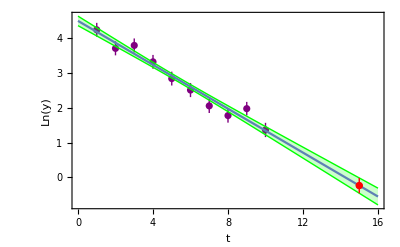

```mathematica
p3=Show[{ListPlot[Log[data],PlotStyle->Purple],ListLinePlot[Table[(alpha+beta z)± σY1[z],{z,0,16,0.1}],IntervalMarkers->"Bands",IntervalMarkersStyle->Green,DataRange->{0,16}],ListPlot[{{15,PlusMinus[f[15],σY1[15]]}},PlotStyle->Red]},PlotRange->All,Frame->True,FrameLabel->{"t","Ln(y)"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

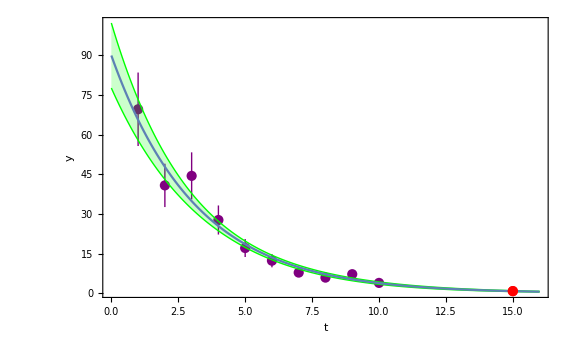

```mathematica
p4 =Show[{ListPlot[data,PlotStyle->Purple],ListLinePlot[Table[E^(alpha+beta z)± σy2[z],{z,0,16,0.1}],IntervalMarkers->"Bands",IntervalMarkersStyle->Green,DataRange->{0,16}],ListPlot[{{15,PlusMinus[fexp[15],σy2[15]]}},PlotStyle->Red]},PlotRange->All,Frame->True,FrameLabel->{"t","y"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

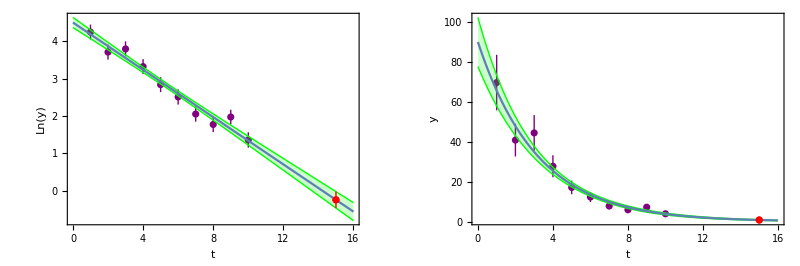

```mathematica
g1=GraphicsRow[{p3 ,p4}]
Export["ex4-2.png",Show[g1,ImageSize->11 inches]];
```

## 5η Άσκηση

Έστω μία ποσότητα y η οποία εξαρτάται γραμμικά από την ποσότητα x: y = α + bx. Υποθέτουμε ότι η αβεβαιότητα στη μέτρηση του y είναι σ = 0.5 (ανεξάρτητη του y). 
a. Να παράξετε και να παραστήσετε γραφικά (με το σφάλμα στο y) ένα σύνολο Ν = 10 τυχαίων ζευγών (x, y), όπου το x είναι ομοιόμορφα κατανεμημένο στο διάστημα [0, 10] και το y ακολουθεί κανονική κατανομή με μέση τιμή μ = −0.5x + 5 και διασπορά σ. 
b. Για το παραπάνω σύνολο τιμών να κάνετε προσαρμογή του μοντέλου y = α + bx με τη μέθοδο ελαχίστων τετραγώνων και να υπολογίσετε τις παραμέτρους του μοντέλου καθώς και τον πίνακα διασποράς τους. 
c. Να επαναλάβετε το ερώτημα (b) χρησιμοποιώντας το μοντέλο y = α + bx + c x^2 (στα ίδιο σύνολο τιμών). Ποιο μοντέλο δίνει καλύτερη προσαρμογή; 
d. Να επαναλάβετε τα βήματα (α) και (β) 10000 φορές και να βρείτε τις κατανομές των παραμέτρων α̂, b̂, των ποσοτήτων (α̂-(α̂)_true)/(σ_(α̂)), (b̂-(b̂)_true)/(σ_(b̂)), (χ^2)_min, καθώς και τις p-value P(χ^2 ≥(χ^2)_min).
e. Να επαναλάβετε όλα τα παραπάνω για σ = 0.1 και για Ν = 20. 
f. Σχολιάστε τα αποτελέσματα.

Λύση

```mathematica
ClearAll["Global`*"];
```

Το ίδιο να γίνει μετά και για σ = 0.1 και για Ν = 20

```mathematica
inches=72;
σY = 0.1; (*0.5 , 0.1*)
N1=20; (*10, 20*)
ei = Table[σY,{i,1,N1}];
w =Table[ 1/(ei[[i]]^2),{i,1,N1}];
X = RandomVariate[UniformDistribution[{0,10}],N1];
Y = Table[RandomVariate[NormalDistribution[−0.5X[[i]]+5,σY]],{i,1,N1}];
data = Table[{X[[i]],PlusMinus[Y[[i]],σY]},{i,1,Length[Y]}];
data1= Table[{X[[i]],Y[[i]]},{i,1,Length[Y]}];
rline = N1 - 2;
rparabola = N1 - 3;
```

Γραφική αναπαράσταση των δεδομένων

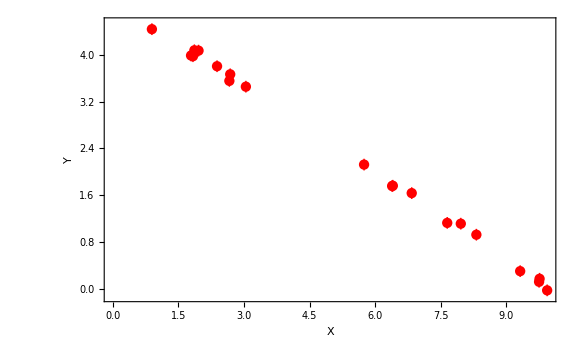

```mathematica
l1=ListPlot[data,PlotRange->Automatic,PlotStyle->Red,Frame->True,FrameLabel->{"Χ","Υ"},LabelStyle->{FontFamily->"Times New Roman",20}]
Export["ex5-1.png",Show[l1,ImageSize->8 inches]];
```

Εύρεση των fits

```mathematica
Clear[a,b,c];
χ2line= Total[w(Y-a-b X)^2];est[x_]:=a +b x/.FindMinimum[χ2line,{a,b}][[2]];
χ2parabola=Total[w(Y-a-b X-c X X)^2];est2[x_]:= a+b x+c x^2 /. FindMinimum[χ2parabola,{a,b,c}][[2]];
```

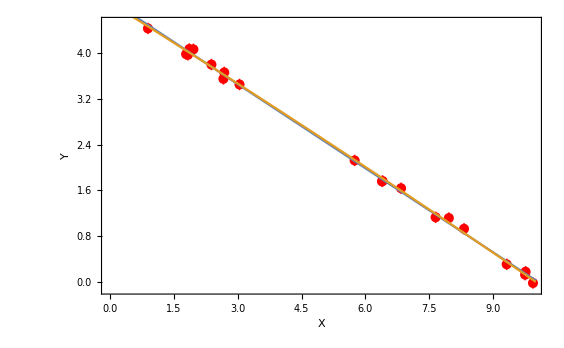

```mathematica
l11=Show[ListPlot[data,PlotRange->Automatic,PlotStyle->Red],Plot[{est[t],est2[t]},{t,0,10}],Frame->True,FrameLabel->{"X","Y"},LabelStyle->{FontFamily->"Times New Roman",20}]
Export["ex5-2.png",Show[l11,ImageSize->8 inches]];
```

Εύρεση των p-values:

```mathematica
SurvivalFunction[ChiSquareDistribution[8],FindMinValue[χ2line,{a,b}]]
```

0.567845

```mathematica
SurvivalFunction[ChiSquareDistribution[7],FindMinValue[χ2parabola,{a,b,c}]]
```

0.508318

Έλεγχος καλύτερης προσαρμογής:

```mathematica
FindMinValue[χ2line,{a,b}]/rline
```

0.372967

```mathematica
FindMinValue[χ2parabola,{a,b,c}]/rparabola
```

0.36897

Εύρεση του πίνακα συνδιασποράς:

```mathematica
line=LinearModelFit[data1,{1,x},x,Weights->w];
parabola=NonlinearModelFit[data1,α+b*x+c x^2,{α,b,c},x,Weights->w];
```

```mathematica
Vline = line["CovarianceMatrix"]//MatrixForm
```

(0.000727158 | -0.000100909
-0.000100909 | 0.0000188333)

```mathematica
Vparabola = parabola["CovarianceMatrix"]//MatrixForm
```

(0.00254648 | -0.00109307 | 0.0000905115
-0.00109307 | 0.000558563 | -0.0000492028
0.0000905115 | -0.0000492028 | 4.48373×10^-6)

Επανάληψη για 10.000

```mathematica
XDD= ParallelTable[RandomVariate[UniformDistribution[{0,10}],N1],{i,1,10000}];
```

```mathematica
YDD=ParallelTable[RandomVariate[NormalDistribution[-0.5 XDD[[i]][[j]] +5, σY]],{i,1,10000},{j,1,N1}];
```

```mathematica
data5D=ParallelTable[{XDD[[i]][[j]],YDD[[i]][[j]]},{i,1,10000},{j,1,N1}];
```

```mathematica
lines=Table[LinearModelFit[data5D[[i]],{1,x},x],{i,1,10000}];
```

```mathematica
alphas = ParallelTable[lines[[i]]["BestFitParameters"][[1]],{i,1,10000}];
```

```mathematica
betas = ParallelTable[lines[[i]]["BestFitParameters"][[2]],{i,1,10000}];
```

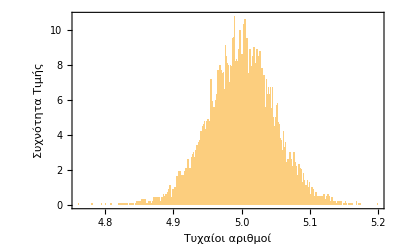

```mathematica
h1 = Histogram[alphas,500,"PDF",Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20},PlotRange->Automatic]
Export["ex5-3.png",Show[h1,ImageSize->8 inches]];
```

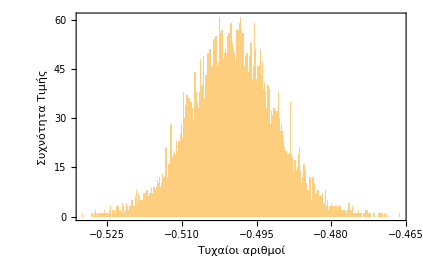

```mathematica
h2 = Histogram[betas,500,"PDF",Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20},PlotRange->Automatic]
Export["ex5-4.png",Show[h2,ImageSize->8 inches]];
```

```mathematica
alphasd=ParallelTable[lines[[i]]["BestFitParameters"][[1]],{i,1,10000}];
betasd= ParallelTable[lines[[i]]["BestFitParameters"][[2]],{i,1,10000}];
```

```mathematica
alphahat =ParallelTable[ (alphasd[[i]] -Mean[alphasd])/StandardDeviation[alphasd],{i,1,10000}];
```

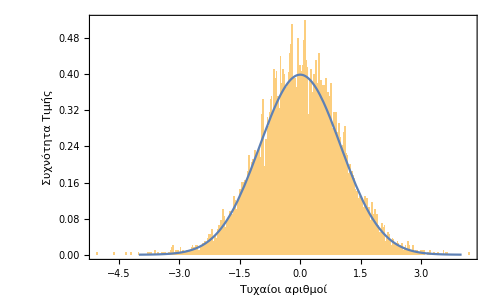

```mathematica
h3=Show[{Histogram[alphahat,500,"PDF",Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20},PlotRange->Automatic],Plot[PDF[NormalDistribution[],x],{x,-4,4}]}]
Export["ex5-5.png",Show[h3,ImageSize->8 inches]];
```

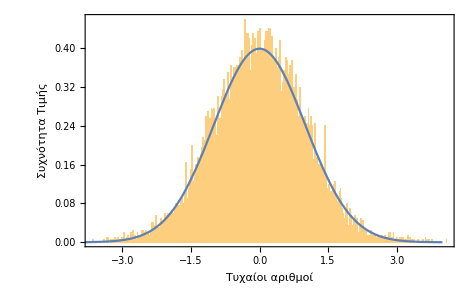

```mathematica
betahat =ParallelTable[ (betasd[[i]] -Mean[betasd])/StandardDeviation[betasd],{i,1,10000}];
h4=Show[{Histogram[betahat,500,"PDF",Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20},PlotRange->Automatic],Plot[PDF[NormalDistribution[],x],{x,-4,4}]}]
Export["ex5-6.png",Show[h4,ImageSize->8 inches]];
```

```mathematica
χ2min=Table[x=RandomVariate[UniformDistribution[{0,10}],N1];y=Table[RandomVariate[NormalDistribution[-0.5 x[[i]] +5, σY]],{i,N1}];FindMinValue[Total[w(y-a-b x)^2],{a,b}],{i,10000}];
```

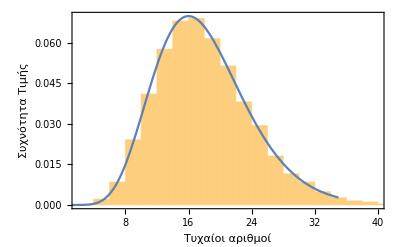

```mathematica
h5=Show[{Histogram[χ2min,Automatic,"PDF",Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}],Plot[PDF[ChiSquareDistribution[rline],x],{x,0,35}]}]
Export["ex5-7.png",Show[h5,ImageSize->8 inches]];
```

Εύρεση του p-value:

```mathematica
pvalues=Table[x=RandomVariate[UniformDistribution[{0,10}],N1];y=Table[RandomVariate[NormalDistribution[-0.5 x[[i]] +5, σY]],{i,N1}];SurvivalFunction[ChiSquareDistribution[rline],FindMinValue[Total[w(y-a-b x)^2],{a,b}]],{i,10000}];
```

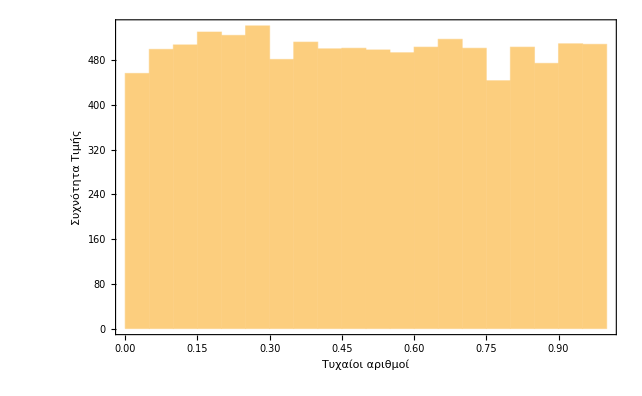

```mathematica
h6=Histogram[pvalues,Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
Export["ex5-8.png",Show[h6,ImageSize->8 inches]];
```